# Name |

## Wolf Pics

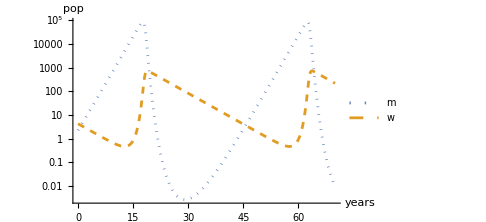

MW.jpg

```mathematica
{α,γ}=N[{2/3 -1/20,1/5}];
{β,δ}={α/100,γ/5000};
TMax=70;
{w0,m0}={4.3,2.3};
{mSol,wSol}=NDSolveValue[{
m'[t]==α m[t]-β m[t]*w[t], m[0]==m0,
w'[t]==-γ w[t]+δ m[t]*w[t], w[0]==w0
 },{m,w},{t,0, TMax}];
Pic=LogPlot[{mSol[t],wSol[t]},{t,0,TMax},
ImageSize->Medium,PlotStyle->{Dotted,Dashed},
AxesLabel->{"years","pop"},PlotLegends->{"m","w"}]
Export["MW.jpg",Pic]
```

## Tanks

### HW

Our HW tank problem from week 8 was

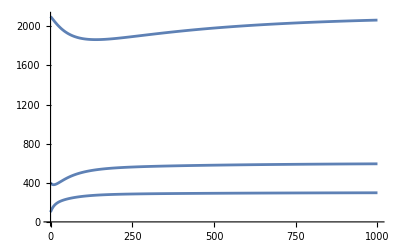

{-0.101375,-0.0170214,-0.00231811}

```mathematica
A={
{-7/100,5/200,0},
{7/100,-9/200,2/700},
{0.0,4/200,-4/700}
};
f={6,0,0};
y0={100,400,2100};
TMax=1000;
ySol=NDSolveValue[{y'[t]==A.y[t]+f,y[0]==y0},y,{t, 0, TMax}];
Plot[ySol[t],{t,0, TMax}]
Eigenvalues[A]
```

We would like to understand this behavior.

### HW

Our practice tank problem from week 8 was

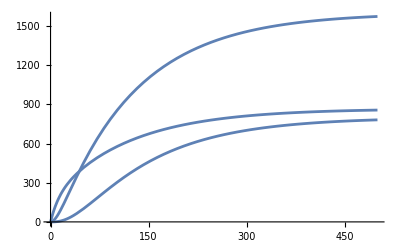

{-0.0847851,-0.0318944,-0.00832048}

```mathematica
A={
{-6/100,4/200,0},
{6/100,-7/200,1/200},
{0.0,3/200,-3/100}
};
f={20,0,0};
y0={0,0,0};
TMax=500;
ySol=NDSolveValue[{y'[t]==A.y[t]+f,y[0]==y0},y,{t, 0, TMax}];
Plot[ySol[t],{t,0, TMax}]
Eigenvalues[A]
```

We would like to understand this behavior.